```mathematica
(* NOTE My work starts below under the section labeled Extra Credit.  The coding before that is from the Instructor, David Meretzky. *)

(*  Here we simulate fluid flow through a blocked pipe
Below is the potential function    *)
```

```mathematica
u[x_,y_]:= x + x/(x^2 + y^2)
```

```mathematica
(* Below is a plot of the potential function *)
```

```mathematica
Plot3D[u[x,y],{x,-4,4},{y,0,2}]
```

-Graphics3D-

```mathematica
(*  
         d= {(x,y)|-2 ≤ x ≤ 2;0 ≤ y ≤ 2} 
*)
```

```mathematica
dx = .2;
dy = .2;
d = {};
```

```mathematica
(* Our interval in the x direction is of length 4. The partition size in the x direction is dx thus the number of intervals is calculated as below:  *)
```

```mathematica
4/dx
```

20.

```mathematica
For[i =1, i ≤ 4/dx, i++,

For[j =1, j ≤ 2/dy, j++,

x = -2 + dx * i ;
y = 0 + dy*j;

AppendTo[d, {x,y}]

]
]
```

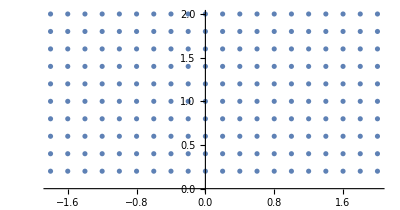

```mathematica
ListPlot[d, AspectRatio->Automatic]
```

```mathematica
(* 
 Here is another version of the above code except we remove points to create the obstruction with the If statement:
*)
```

```mathematica
d = {};

For[i =1, i ≤ 4/dx, i++,
For[j =1, j ≤ 2/dy, j++,

x = -2 + dx * i ;
y = dy*j;

If[x ^2 + y^2  ≥  1, 
AppendTo[d, {x,y}]
]

]
]
```

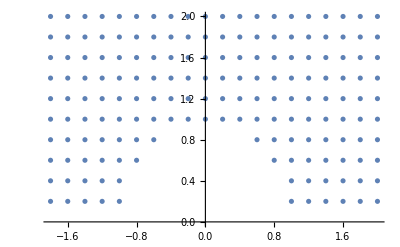

```mathematica
ListPlot[d]
```

```mathematica
Clear[x,y, dudx, dudy]
```

```mathematica
u[x,y]
```

x+x/(x^2+y^2)

```mathematica
(* As an exercise for extra points you can compute the gradients using forward or backwards or central differences. *)
```

```mathematica
dudx[{x_,y_}] = D[u[x,y], x]
```

1-(2 x^2)/((x^2+y^2)^2)+1/(x^2+y^2)

```mathematica
dudy[{x_,y_}] = D[u[x,y], y]
```

-(2 x y)/((x^2+y^2)^2)

```mathematica
(* d is again just a long list of points *)
```

```mathematica
d
```

{{-1.8,0.2},{-1.8,0.4},{-1.8,0.6},{-1.8,0.8},{-1.8,1.},{-1.8,1.2},{-1.8,1.4},{-1.8,1.6},{-1.8,1.8},{-1.8,2.},{-1.6,0.2},{-1.6,0.4},{-1.6,0.6},{-1.6,0.8},{-1.6,1.},{-1.6,1.2},{-1.6,1.4},{-1.6,1.6},{-1.6,1.8},{-1.6,2.},{-1.4,0.2},{-1.4,0.4},{-1.4,0.6},{-1.4,0.8},{-1.4,1.},{-1.4,1.2},{-1.4,1.4},{-1.4,1.6},{-1.4,1.8},{-1.4,2.},{-1.2,0.2},{-1.2,0.4},{-1.2,0.6},{-1.2,0.8},{-1.2,1.},{-1.2,1.2},{-1.2,1.4},{-1.2,1.6},{-1.2,1.8},{-1.2,2.},{-1.,0.2},{-1.,0.4},{-1.,0.6},{-1.,0.8},{-1.,1.},{-1.,1.2},{-1.,1.4},{-1.,1.6},{-1.,1.8},{-1.,2.},{-0.8,0.6},{-0.8,0.8},{-0.8,1.},{-0.8,1.2},{-0.8,1.4},{-0.8,1.6},{-0.8,1.8},{-0.8,2.},{-0.6,0.8},{-0.6,1.},{-0.6,1.2},{-0.6,1.4},{-0.6,1.6},{-0.6,1.8},{-0.6,2.},{-0.4,1.},{-0.4,1.2},{-0.4,1.4},{-0.4,1.6},{-0.4,1.8},{-0.4,2.},{-0.2,1.},{-0.2,1.2},{-0.2,1.4},{-0.2,1.6},{-0.2,1.8},{-0.2,2.},{0.,1.},{0.,1.2},{0.,1.4},{0.,1.6},{0.,1.8},{0.,2.},{0.2,1.},{0.2,1.2},{0.2,1.4},{0.2,1.6},{0.2,1.8},{0.2,2.},{0.4,1.},{0.4,1.2},{0.4,1.4},{0.4,1.6},{0.4,1.8},{0.4,2.},{0.6,0.8},{0.6,1.},{0.6,1.2},{0.6,1.4},{0.6,1.6},{0.6,1.8},{0.6,2.},{0.8,0.6},{0.8,0.8},{0.8,1.},{0.8,1.2},{0.8,1.4},{0.8,1.6},{0.8,1.8},{0.8,2.},{1.,0.2},{1.,0.4},{1.,0.6},{1.,0.8},{1.,1.},{1.,1.2},{1.,1.4},{1.,1.6},{1.,1.8},{1.,2.},{1.2,0.2},{1.2,0.4},{1.2,0.6},{1.2,0.8},{1.2,1.},{1.2,1.2},{1.2,1.4},{1.2,1.6},{1.2,1.8},{1.2,2.},{1.4,0.2},{1.4,0.4},{1.4,0.6},{1.4,0.8},{1.4,1.},{1.4,1.2},{1.4,1.4},{1.4,1.6},{1.4,1.8},{1.4,2.},{1.6,0.2},{1.6,0.4},{1.6,0.6},{1.6,0.8},{1.6,1.},{1.6,1.2},{1.6,1.4},{1.6,1.6},{1.6,1.8},{1.6,2.},{1.8,0.2},{1.8,0.4},{1.8,0.6},{1.8,0.8},{1.8,1.},{1.8,1.2},{1.8,1.4},{1.8,1.6},{1.8,1.8},{1.8,2.},{2.,0.2},{2.,0.4},{2.,0.6},{2.,0.8},{2.,1.},{2.,1.2},{2.,1.4},{2.,1.6},{2.,1.8},{2.,2.}}

```mathematica
Length[d]
```

170

```mathematica
(* Visualization Code *)
```

```mathematica
arrows = {};

For[i = 1, i ≤ Length[d], ++i, 
start = d[[i]];
end = d[[i]] + .2*{dudx[d[[i]]],dudy[d[[i]]]};

arrow = Arrow[{start,end}];
AppendTo[arrows,arrow ];
]
```

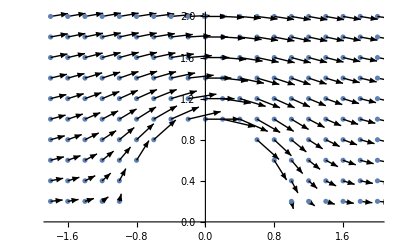

```mathematica
Show[ListPlot[d],Graphics[arrows]]
```

```mathematica
d
```

{{-1.8,0.2},{-1.8,0.4},{-1.8,0.6},{-1.8,0.8},{-1.8,1.},{-1.8,1.2},{-1.8,1.4},{-1.8,1.6},{-1.8,1.8},{-1.8,2.},{-1.6,0.2},{-1.6,0.4},{-1.6,0.6},{-1.6,0.8},{-1.6,1.},{-1.6,1.2},{-1.6,1.4},{-1.6,1.6},{-1.6,1.8},{-1.6,2.},{-1.4,0.2},{-1.4,0.4},{-1.4,0.6},{-1.4,0.8},{-1.4,1.},{-1.4,1.2},{-1.4,1.4},{-1.4,1.6},{-1.4,1.8},{-1.4,2.},{-1.2,0.2},{-1.2,0.4},{-1.2,0.6},{-1.2,0.8},{-1.2,1.},{-1.2,1.2},{-1.2,1.4},{-1.2,1.6},{-1.2,1.8},{-1.2,2.},{-1.,0.2},{-1.,0.4},{-1.,0.6},{-1.,0.8},{-1.,1.},{-1.,1.2},{-1.,1.4},{-1.,1.6},{-1.,1.8},{-1.,2.},{-0.8,0.6},{-0.8,0.8},{-0.8,1.},{-0.8,1.2},{-0.8,1.4},{-0.8,1.6},{-0.8,1.8},{-0.8,2.},{-0.6,0.8},{-0.6,1.},{-0.6,1.2},{-0.6,1.4},{-0.6,1.6},{-0.6,1.8},{-0.6,2.},{-0.4,1.},{-0.4,1.2},{-0.4,1.4},{-0.4,1.6},{-0.4,1.8},{-0.4,2.},{-0.2,1.},{-0.2,1.2},{-0.2,1.4},{-0.2,1.6},{-0.2,1.8},{-0.2,2.},{0.,1.},{0.,1.2},{0.,1.4},{0.,1.6},{0.,1.8},{0.,2.},{0.2,1.},{0.2,1.2},{0.2,1.4},{0.2,1.6},{0.2,1.8},{0.2,2.},{0.4,1.},{0.4,1.2},{0.4,1.4},{0.4,1.6},{0.4,1.8},{0.4,2.},{0.6,0.8},{0.6,1.},{0.6,1.2},{0.6,1.4},{0.6,1.6},{0.6,1.8},{0.6,2.},{0.8,0.6},{0.8,0.8},{0.8,1.},{0.8,1.2},{0.8,1.4},{0.8,1.6},{0.8,1.8},{0.8,2.},{1.,0.2},{1.,0.4},{1.,0.6},{1.,0.8},{1.,1.},{1.,1.2},{1.,1.4},{1.,1.6},{1.,1.8},{1.,2.},{1.2,0.2},{1.2,0.4},{1.2,0.6},{1.2,0.8},{1.2,1.},{1.2,1.2},{1.2,1.4},{1.2,1.6},{1.2,1.8},{1.2,2.},{1.4,0.2},{1.4,0.4},{1.4,0.6},{1.4,0.8},{1.4,1.},{1.4,1.2},{1.4,1.4},{1.4,1.6},{1.4,1.8},{1.4,2.},{1.6,0.2},{1.6,0.4},{1.6,0.6},{1.6,0.8},{1.6,1.},{1.6,1.2},{1.6,1.4},{1.6,1.6},{1.6,1.8},{1.6,2.},{1.8,0.2},{1.8,0.4},{1.8,0.6},{1.8,0.8},{1.8,1.},{1.8,1.2},{1.8,1.4},{1.8,1.6},{1.8,1.8},{1.8,2.},{2.,0.2},{2.,0.4},{2.,0.6},{2.,0.8},{2.,1.},{2.,1.2},{2.,1.4},{2.,1.6},{2.,1.8},{2.,2.}}

```mathematica
(* Extra Credit *)

(* True values using dudx, dudy as calculated above, over d. *)

truegrad={};

For[i=1,i≤Length[d],++i,
AppendTo[truegrad,{dudx[{d[[i]][[1]],d[[i]][[2]]}],dudy[{d[[i]][[1]],d[[i]][[2]]}]}]
];

(* First Forward Difference *)

ffwddiff={};

For[i=1,i≤Length[d],++i,
AppendTo[ffwddiff,{(u[d[[i]][[1]]+dx,d[[i]][[2]]]-u[d[[i]][[1]],d[[i]][[2]]])/dx,
(u[d[[i]][[1]],d[[i]][[2]]+dy]-u[d[[i]][[1]],d[[i]][[2]]])/dy}]
];

(* Mean Square Error for First Forward Difference *)
Norm[truegrad-ffwddiff]/Norm[truegrad]
```

0.0620067

```mathematica
(* First Backward Difference *)

fbckwddiff={};

For[i=1,i≤Length[d],++i,
AppendTo[fbckwddiff,{(u[d[[i]][[1]],d[[i]][[2]]]-u[d[[i]][[1]]-dx,d[[i]][[2]]])/dx,(u[d[[i]][[1]],d[[i]][[2]]]-u[d[[i]][[1]],d[[i]][[2]]-dy])/dy}]
];

(* Mean Square Error for First Backward Difference *)
Norm[truegrad-fbckwddiff]/Norm[truegrad]
```

0.0702871

```mathematica
(* First Central Difference *)

fcentdiff={};

For[i=1,i≤Length[d],++i,
AppendTo[fcentdiff,{(u[d[[i]][[1]]+dx,d[[i]][[2]]]-u[d[[i]][[1]]-dx,d[[i]][[2]]])/(2*dx),(u[d[[i]][[1]],d[[i]][[2]]+dy]-u[d[[i]][[1]],d[[i]][[2]]-dy])/(2*dy)}]
];

(* Mean Square Error for First Central Difference *)
Norm[truegrad-fcentdiff]/Norm[truegrad]
```

0.00851309

```mathematica
(* Finding the true uxx and uyy and then calculating uxx+uyy over d.  We can see that the maximum absolute value of uxx+uyy evaluated over all points in d is 1.11022 x 10^-15, so uxx + uyy = 0, as expected *)

dudxdx[{x_,y_}]=D[u[x,y],{x,2}];
dudydy[{x_,y_}]=D[u[x,y],{y,2}];
f[{x_,y_}]=dudxdx[{x,y}]+dudydy[{x,y}];
```

```mathematica
values={};
For[i=1,i≤Length[d],++i,
AppendTo[values,f[{d[[i]][[1]],d[[i]][[2]]}]]
];
Max[Abs[values]]
```

1.11022×10^-15

```mathematica
(* Second Central Difference. *)

seccentdiff={};

For[i=1,i≤Length[d],++i,
AppendTo[seccentdiff,{(u[d[[i]][[1]]+dx,d[[i]][[2]]]-2*u[d[[i]][[1]],d[[i]][[2]]]+u[d[[i]][[1]]-dx,d[[i]][[2]]])/dx^2,(u[d[[i]][[1]],d[[i]][[2]]+dy]-2*u[d[[i]][[1]],d[[i]][[2]]]+u[d[[i]][[1]],d[[i]][[2]]-dy])/dy^2}]
];

(* Adding our estimates of uxx and uyy for values over d, we expect uxx + uyy to be approximately equal to zero.  We see that the greatest absolute value of the output of the estimated uxx+uyy over d is .159314, and the smallest is 0, so the estimates provide a fairly good approximation of the true uxx and uyy *)

uxxplusuyy={};

For[i=1,i≤Length[seccentdiff],++i,
AppendTo[uxxplusuyy,seccentdiff[[i]][[1]]+seccentdiff[[i]][[2]]]
];
Max[Abs[uxxplusuyy]]
Min[Abs[uxxplusuyy]]
```

0.159314

0.